# Report: Project 2

Course code: II1303
Date: 2022-12-10

Anton Herdin Ringstedt, antonhr@kth.se
Hein Lee, hein@kth.se
Muttakin Karim, muttakin@kth.se

# Part 1:

## Summary

### Task

H  (z)=((1-z^-1)∏_(k=1)^4 (1-z^-1 ⅇ^(-j0.11π(2k-1)))(1-z^-1 ⅇ^(j0.11π(2k-1))))/(100∏_(k=1)^4 (1-0.9 z^-1 ⅇ^(-j 0.22π k))(1-0.9 z^-1 ⅇ^(j0.22π k)))

a) Make a pole-zero plot of H(z). Is the system stable?
b) Discuss how the filter works, what happens with certain frequencies?
c) Illustrate the frequency response of the IIR filter!
d) Sketch a direct form structure to illustrate the IIR filter!
e) Consider the continuous signal x(t) defined as:

x(t)=1/π∑_(k=1)^9 (-1)^(k -1)/k Sin(2π f_0 k t)

with f_0 = 220 Hz. This signal is sampled with the frequency f_s = 4 kHz. Plot the sampled signal x[n]!
f) Now, the sampled signal x[n] is input to the IIR filter above. Compute and plot the output signal y[n]!
g) Draw and compare the two-sided spectrum of x[n] and that of y[n]!

### Result

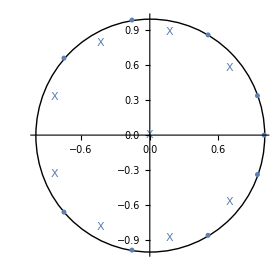
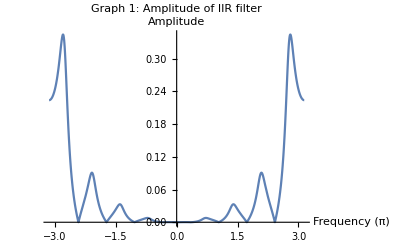
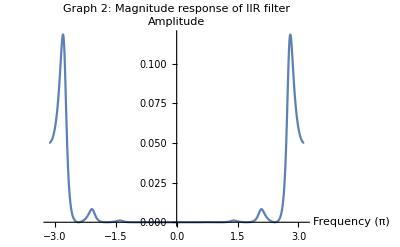
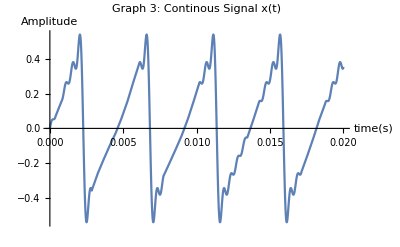
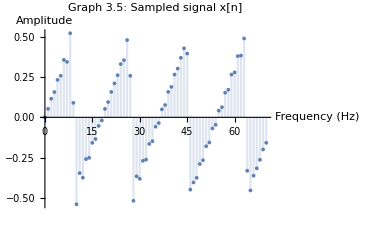
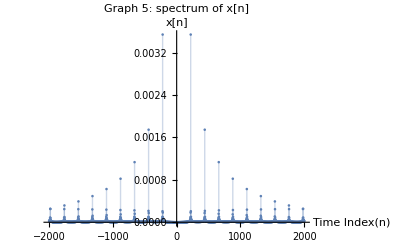
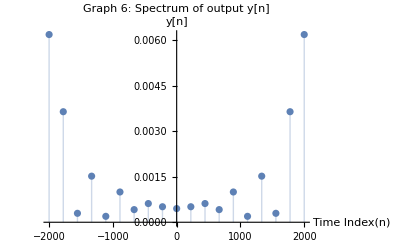
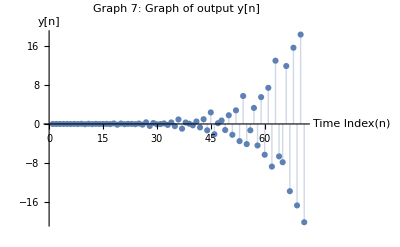
-Graphics-


-Graphics3D-

"b0" | 1
"b1" | -2.09
"b2" | 2.21
"b3" | -2.28
"b4" | 2.3
"b5" | -2.3
"b6" | 2.28
"b7" | -2.21
"b8" | 2.09
"b9" | -1	"a0" | 1
"a1" | 0.82
"a2" | 0.78
"a3" | 0.67
"a4" | 0.63
"a5" | 0.54
"a6" | 0.51
"a7" | 0.43
"a8" | 0.43


-Graphics-


-Graphics-
-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-


-Graphics-

-Graphics-

## Explaining the methods

First, the IIR filter equation was broken up into two separate parts, B(z) and 1/(A(z))where B(z) is the feed-forward part, and 1/(A(z)) is the feedback part. From this, the individual poles and zeroes could be plotted out on the complex plane. TransferFunctionCancels removes common poles and zeroes in the model. TransferFunctionZeroes and TransferFunctionPoles are the ones that acquire the coordinates of the poles/zeroes on the complex plane.

func = TransferFunctionCancel[TransferFunctionModel[Hz, z]];
 
zeroes = Flatten[TransferFunctionZeros[func]]; 

poles = Flatten[TransferFunctionPoles[func]]; 

In order to properly filter our input x[n]=1/π∑_(k=1)^9 (-1)^(k -1)/k Sin[2π f0 / fs k n ] with the IIR filter H(Z) the function RecurrenceFilter is used. The function is specifically designed to take a discrete input and apply the IIR filter to it, this gives the output y[n]. To plot the spectrum of the output signal y[n] the Mathematica function Fourier, which finds the fourier transform of discrete signals, is used. This allows for the generation of a list containing the fourier transform of the discrete input values. These can then be put into a ListPlot to get out the actual spectrum. 

YOut[x_]:=RecurrenceFilter[HZ,Table[xn[n],{n,-x,x}]]

Fourier[YOut[x]];

However this wouldn’t actually give out the spectrum as one would expect, therefor a version of the function that can be created in MATLAB, fftshift() can be implemented here in order to fix this issue. This function was found on the Mathematica section on StackExchange. [StackExchange: https://mathematica.stackexchange.com/questions/33574/whats-the-correct-way-to-shift-zero-frequency-to-the-center-of-a-fourier-transf, {last modified on October, 2013}]
	This function limits the output of the discrete fourier transform and flips it to form a complete true spectrum. The results of fftshift were compared to that of x[n] as a spectrum made with FourierCoefficient. Which is another built in way to get the spectrum, but which would take to long to use on the actual output y[n] which is why an alternate method was located. The results given by FourierCoefficient closely matched the results given by the method using Fourier and fftshift on x[n]. This together with ListPlot formed the finished spectrum of the output signal y[n]. 

fftshift[dat_? ArrayQ, k: (_Integer? Positive|All):All]:=Module[{dims=Dimensions[dat]},
RotateRight[dat,If[k===All,Quotient[dims,2],Quotient[dims[[k]],2] UnitVector[Length[dims],k]]]]

ListPlot[Abs[fftshift[%]/Length[%]],DataRange->{-1/(2 h),1/(2h)},PlotRange->All,Filling->Axis]

## Discussing the results

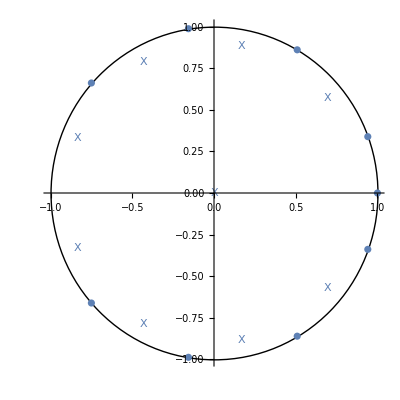
This figure represents the pole-zero plot of the IIR filter H(Z). A stable IIR system is defined as a system were all its poles lie within the unit circle. This can be verified by looking at the “X”es of the figure and noting that all of them lie in the unit circle. However, a more precise method of determining the stability by using the definition, ∑_(m=0)^∞ |h[m]|<∞, which more accurately shows if the system is stable or not. 
	This filter is a High-pass filter with some band pass qualities, amplifying higher frequencies, but also amplifying certain  other frequencies. Most zeroes lay with  (2π k)/9 radians apart. One zero is missing at (10π)/9  rad and there is an extra zero at 0/2π rad. For the poles, most also lay (2π k+9π)/9radians apart, meaning the difference is that they are flipped compared to the zeroes. One pole is missing at 0/2π rad. This makes the function of the filter: 
Pulls down signals with ω values of 0/2π rad and (2π k)/9, excluding (10π)/9. 
Pulls up signals with ω values of (2π k)/9+π =(2π k+9π)/9, excluding (19 π)/9.
This will cause most lower frequencies to be pulled down to zero, but the poles will start pulling up the frequencies as they increase, and on high frequencies they stop getting pulled to zero. 

-Graphics-
By looking at the Amplitude of the frequency response of the filter, these interpretations of the poles and zeroes appear to be accurate. With pull ups and pull downs at the ω  values noted above.
-Graphics-
The next section is about the plotting and comparing of the input and output to the IIR filter. The input to the filter is the continuous signal x(t)=1/π∑_(k=1)^9 (-1)^(k -1)/k Sin[440π  k t]  stampeded at the rate 4000 Hz. The spectrum of the discrete signal x[n] is plotted below, and clearly shows the spectrum lines of the nine different sinusoids in the summation. The IIR filter H(z) will take the higher frequencies of x[n] and amplify them in different bands, and the lower frequencies will be decreased in bands as shown by the explanation of the poles and zeros of the unit circle. 

-Graphics-
When looking at the spectrum of the filtered output y[n] the effects of the filter can clearly be seen as lower frequency signals had their amplitudes dropped, and higher frequency signals had their amplitudes raised. This also shows how certain frequencies in the mid range were also pulled downwards because of the positions of the zeroes in the filter. 

-Graphics-

## Code section

```mathematica
Hz=((1-z^-1)∏_(k=1)^4 (1-z^-1 ⅇ^(-ⅈ 0.11π(2 k -1)))(1-z^-1 ⅇ^(ⅈ 0.11π(2 k -1))))/(100 ∏_(k=1)^4 (1-0.9 z^-1 ⅇ^(-ⅈ 0.22π k))(1-0.9 z^-1 ⅇ^(ⅈ 0.22π k)));(*IIR filter*)
```

```mathematica
HZ=TransferFunctionModel[{{{BZ}},AZ},z,SamplingPeriod->1];(*function defined as model*)
```

```mathematica
(************************************** a ********************************************)
```

```mathematica
ComplexPlot3D[Hz,{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
func=TransferFunctionCancel[TransferFunctionModel[Hz,z]]; (*define*)
```

```mathematica
zeroes=Flatten@TransferFunctionZeros[func] (*Find zeroes of H(z)*)
```

{-0.750111-0.661312 ⅈ,-0.750111+0.661312 ⅈ,-0.156434-0.987688 ⅈ,-0.156434+0.987688 ⅈ,0.509041-0.860742 ⅈ,0.509041+0.860742 ⅈ,0.940881-0.338738 ⅈ,0.940881+0.338738 ⅈ,1.}

```mathematica
poles=Flatten@TransferFunctionPoles[func](*Find poles of H(z)*)
```

{-0.836799-0.331312 ⅈ,-0.836799+0.331312 ⅈ,-0.433578-0.788676 ⅈ,-0.433578+0.788676 ⅈ,0,0.168643-0.884059 ⅈ,0.168643+0.884059 ⅈ,0.693462-0.573682 ⅈ,0.693462+0.573682 ⅈ}

```mathematica
Zeroplot=ComplexListPlot[zeroes];
Poleplot=ComplexListPlot[poles,PlotMarkers->{"X"}];
uint=Graphics[Circle[{0,0},1]];
Show[Poleplot,uint,Zeroplot,PlotRange->Full] (*Plot the zeroes and poles on complex plain*)
```

-Graphics-

```mathematica
(******************************** DIREKT FORM *********************************)
```

```mathematica
Bz=TrigToExp[Simplify[(1-z)∏_(k=1)^4 (1-z ⅇ^(-ⅈ 0.11π(2 k -1)))(1-z ⅇ^(ⅈ 0.11π(2 k -1)))]];(*B(z)*)
```

```mathematica
BZ=1-(2.0867533000678122) z+(2.214233381728728) z^2-(2.2753481956589496) z^3+(2.3020477614440864) z^4-(2.3020477614440793) z^5+(2.2753481956589523) z^6-(2.214233381728726) z^7+(2.0867533000678113) z^8-(0.9999999999999997) z^9
```

1-2.08675 z+2.21423 z^2-2.27535 z^3+2.30205 z^4-2.30205 z^5+2.27535 z^6-2.21423 z^7+2.08675 z^8-1. z^9

```mathematica
Az=TrigToExp[Simplify[ ∏_(k=1)^4 (1-0.9z ⅇ^(-ⅈ 0.22π k))(1-0.9z ⅇ^(ⅈ 0.22π k))] ](*1/(A(z))*)
```

1+(0.816544+0. ⅈ) z+(0.778267+5.55112×10^-17 ⅈ) z^2+(0.670446+0. ⅈ) z^3+(0.627484+5.55112×10^-17 ⅈ) z^4+(0.543061-5.55112×10^-17 ⅈ) z^5+(0.510621-1.94289×10^-16 ⅈ) z^6+(0.433945-1.11022×10^-16 ⅈ) z^7+(0.430467-2.77556×10^-17 ⅈ) z^8

```mathematica
AZ=1+(0.8165440847312153) z+(0.7782673256314596) z^2+(0.6704460790461787) z^3+(0.6274839925063553) z^4+(0.5430613240274034) z^5+(0.5106211923467996) z^6+(0.43394500493364124) z^7+(0.43046721) z^8
```

1+0.816544 z+0.778267 z^2+0.670446 z^3+0.627484 z^4+0.543061 z^5+0.510621 z^6+0.433945 z^7+0.430467 z^8

```mathematica
m1={{"b0",1},{"b1",-2.09},{"b2",2.21},{"b3",-2.28},{"b4",2.30},{"b5",-2.30},{"b6",2.28},{"b7",-2.21},{"b8",2.09},{"b9",-1}};
Grid[m1,Frame->All](*grid for direkt form coefficients b0-b9*)
```

b0 | 1
b1 | -2.09
b2 | 2.21
b3 | -2.28
b4 | 2.3
b5 | -2.3
b6 | 2.28
b7 | -2.21
b8 | 2.09
b9 | -1

```mathematica
m2={{"a0",1},{"a1",.82},{"a2",.78},{"a3",.67},{"a4",.63},{"a5",.54},{"a6",.51},{"a7",.43},{"a8",.43}};
Grid[m2,Frame->All](*grid for direkt form coefficients a0-a8*)
```

a0 | 1
a1 | 0.82
a2 | 0.78
a3 | 0.67
a4 | 0.63
a5 | 0.54
a6 | 0.51
a7 | 0.43
a8 | 0.43

```mathematica
(************************************** c ********************************************)
```

```mathematica
he[x_]:=((1-ⅇ^(-ⅈ x))∏_(k=1)^4 (1-ⅇ^(-ⅈ x)ⅇ^(-ⅈ 0.11π(2 k -1)))(1-ⅇ^(-ⅈ x)ⅇ^(ⅈ 0.11π(2 k -1))))/(100 ∏_(k=1)^4 (1-0.9 ⅇ^(-ⅈ x)ⅇ^(-ⅈ 0.22π k))(1-0.9 ⅇ^(-ⅈ x)ⅇ^(ⅈ 0.22π k)))(*Frequency respons of filter*)
```

```mathematica
mangintude = he[x]*Conjugate[he[x]]; (*filter magnitude*)
```

```mathematica
Plot[Abs[he[x]],{x, -  Pi, Pi},PlotRange->Full,AxesLabel->{"Frequency (π)","Amplitude"}, PlotLabel->"Graph 1: Amplitude of IIR filter " ]
```

-Graphics-

```mathematica
Plot[mangintude,{x, -Pi, Pi},PlotRange->Full, AxesLabel->{"Frequency (π)","Amplitude"}, PlotLabel->"Graph 2: Magnitude response of IIR filter " ]
```

-Graphics-

```mathematica
(************************************** e ********************************************)
```

```mathematica
f0=220; (*Hz*)
```

```mathematica
fs=4000 ;(*Hz sampling rate*)
```

```mathematica
h=1/fs;
```

```mathematica
xf[t_]:=1/π∑_(k=1)^9 (-1)^(k -1)/k Sin[2π f0 k t] (*x(t)*)
```

```mathematica
xn[n_]:=1/π∑_(k=1)^9 (-1)^(k -1)/k Sin[2π f0 / fs k n ] (*x[n]*)
```

```mathematica
Plot[xf[t],{t,0,0.02},AxesLabel->{"time(s)","Amplitude"}, PlotLabel->"Graph 3: Continous Signal x(t)"]
```

-Graphics-

```mathematica
DiscretePlot[xn[n],{n,0,70},AxesLabel->{"Frequency (Hz)","Amplitude"}, PlotLabel->"Graph 3.5: Sampled signal x[n]"]
```

-Graphics-

```mathematica
(************************************** f ********************************************)
```

```mathematica
YOut[x_]:=RecurrenceFilter[HZ,Table[xn[n],{n,-x,x}]](*filtered signal y[n]*)
```

```mathematica
(*fftshift source:*)
```

[StackExchange:
https://mathematica.stackexchange.com/questions/33574/whats-the-correct-way-to-shift-zero-frequency-to-the-center-of-a-fourier-transf
,{last modified on October, 2013}].

```mathematica
fftshift[dat_? ArrayQ, k: (_Integer? Positive|All):All]:=Module[{dims=Dimensions[dat]},RotateRight[dat,If[k===All,Quotient[dims,2],Quotient[dims[[k]],2] UnitVector[Length[dims],k]]]](*shift fourier data*)
```

```mathematica
input=N@ArrayPad[{1},{0,1000},{1}]; (*input array*)
OutputResponse[HZ,input];(*output response of filter*)
Fourier[%];
ListPlot[Abs[fftshift[%]/Length[%]],DataRange->{-1/(2 h),1/(2h)},PlotRange->All,Filling->Axis,AxesLabel->{"Time Index(n)","H(z)"}, PlotLabel->"Graph 4: Frequency spectrum of h(z)"]//Quiet
```

-Graphics-

```mathematica
Table[xn[n],{n,-1000,1000}];
Fourier[%];
ListPlot[Abs[fftshift[%]/Length[%]],DataRange->{-1/(2 h),1/(2h)},PlotRange->All,Filling->Axis,AxesLabel->{"Time Index(n)","x[n]"}, PlotLabel->"Graph 5: spectrum of x[n]"]
```

-Graphics-

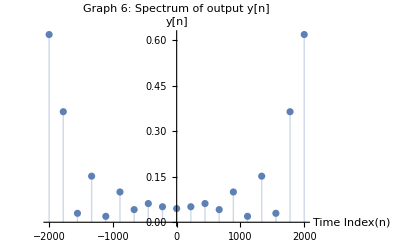

```mathematica
Fourier[YOut[9]];
ListPlot[Abs[fftshift[%]/Length[%]],DataRange->{-1/(2 h),1/(2h)},PlotRange->All,Filling->Axis,AxesLabel->{"Time Index(n)","y[n]"}, PlotLabel->"Graph 6: Spectrum of output y[n]"]
```

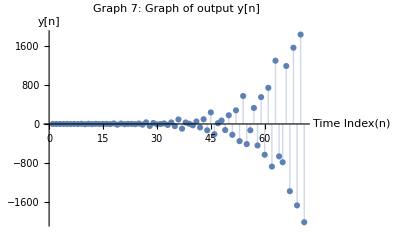

```mathematica
ListPlot[YOut[35],PlotRange->Full,Filling->Axis,AxesLabel->{"Time Index(n)","y[n]"}, PlotLabel->"Graph 7: Graph of output y[n]"]
```

# Part 2:

## Summary

### Task

x(t)=[ⅇ^(-50t)Cos(2 π 100t)+ⅇ^(-75t)Cos(2 π  200t)+ⅇ^(-100t)Cos(2  π 300t)] u(t)

a)  	Make a plot of x(t) as function of time!

b)	Compute the spectrum X(jω)!

c) 	Plot |X(jω)| and arg(X(jω))!

d)	There are some distinct local maxima and minima in the spectrum. Solve for these frequencies!

e)	Can you motivate the local maxima from the expression of x(t)?

### Result

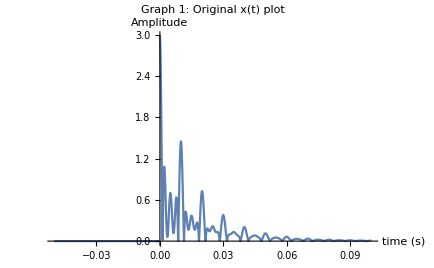

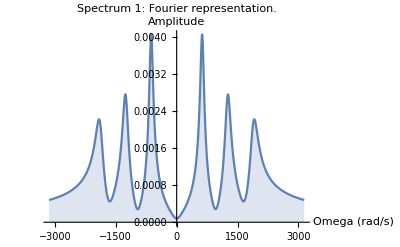
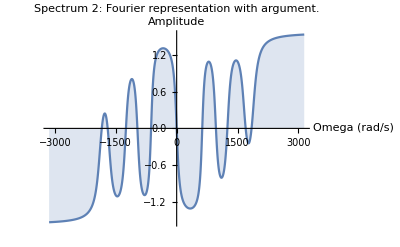
The spectrum of X(jω): ((-50+ⅈ ω)/(-40000 π^2+(50 ⅈ+ω)^2)+(-75+ⅈ ω)/(-160000 π^2+(75 ⅈ+ω)^2)+(-100+ⅈ ω)/(-360000 π^2+(100 ⅈ+ω)^2))/(√(2 π))
-Graphics-
-Graphics-

Maxima: ±100 Hz, ±200 Hz, ±300 Hz.
Minima: 0 Hz, ±150 Hz, ±250 Hz.

## Explaining the methods

Firstly, the unit step of u (t) was calculated by using UnitStep[t] function i Mathematica. This was then multiplied with the rest of the function of continuous signal. This made it possible to plot the graph of x(t). Furthermore, DiscretePlot function was used to draw the spectrum diagrams.  FindMinimum and FindMaximum was then used to calculate the maximum and minimum points of the spectrum and x(t).

## Discussing the results

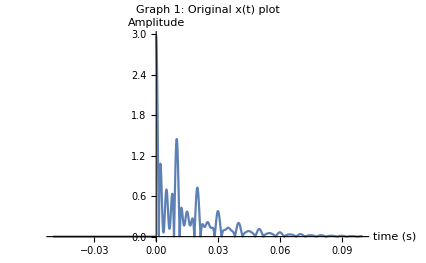

Graph 1 is the graph of the continuous signal x(t) along with the unit step u(t). Unit step would result in zero for the negative values of time and 1 for the positive values of 1. This is phenomena is reflected in the graph. Also the absolute value of the continuous signal was used during plot, this shifted the negative points of x(t) to the positive side. 

The spectrum function was computed using FourierTransform which gave the following result:
 ((-50+ⅈ ω)/(-40000 π^2+(50 ⅈ+ω)^2)+(-75+ⅈ ω)/(-160000 π^2+(75 ⅈ+ω)^2)+(-100+ⅈ ω)/(-360000 π^2+(100 ⅈ+ω)^2))/(√(2 π))
The calculated Fourier transformation was then plotted with a range of -1000π to 1000π which resulted in the following graph:
 -Graphics-

The same Fourier equation was used to construct an argument plot which had the negative amplitudes on one side and the positive amplitude on the other side:




 -Graphics-

From the graph in Spectrum: 1, the maximum and minimum amplitudes could be figured out as the range for ω was set from -1000π to 1000π.
By analysing the original x(t) function, it can be noted that the local maxima corresponds to the frequency in the cosines. If the first maxima is at 0.00406 at 627 rad/s, which corresponds to 100 Hz, just as the first cosine. Therefor it is logical to conclude that the rest of the maxima are at the other cosine frequencies. This also means that the minima which lay between the maxima, could be calculated. The minima was calculated by finding the center between two peaks since the graph is symmetric.
Maxima: ±100 Hz, ±200 Hz, ±300 Hz.
Minima: 0 Hz, ±150 Hz, ±250 Hz.

## Code section

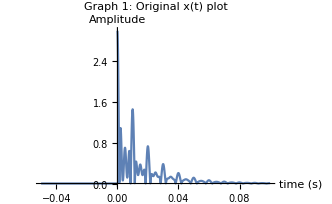

```mathematica
(***************************a********************************)
u[t_]:=UnitStep[t]; (*converting to unit step*)
u[t];
x[t_]:=(ⅇ^(-50t)Cos[2 π 100t]+ⅇ^(-75t)Cos[2 π  200t]+ⅇ^(-100t)Cos[2  π 300t]) u[t];
x[t];
Plot[Abs[x[t]],{t,-0.05,0.1}, PlotRange->Full,AxesLabel->{"time (s)","Amplitude"}, PlotLabel->"Graph 1: Original x(t) plot" ]
```

```mathematica
(**************************b***********************************)
X[ω_]=FourierTransform[x[t],t,ω] (*Computing the spectrum*)
```

((-50+ⅈ ω)/(-40000 π^2+(50 ⅈ+ω)^2)+(-75+ⅈ ω)/(-160000 π^2+(75 ⅈ+ω)^2)+(-100+ⅈ ω)/(-360000 π^2+(100 ⅈ+ω)^2))/(√(2 π))

```mathematica
(**************c*****************)

DiscretePlot[Abs[X[ω]],{ω,-1000π,1000π},AxesLabel->{"Omega (rad/s)","Amplitude"}, PlotLabel->"Spectrum 1: Fourier representation."](*Discrete plot with 200pi*)
```

-Graphics-

```mathematica
DiscretePlot[Arg[X[ω]],{ω,-1000π,1000π}, AxesLabel->{"Omega (rad/s)","Amplitude"}, PlotLabel->"Spectrum 2: Fourier representation with argument." ](*Argument plot with 200pi*)
```

-Graphics-

```mathematica
(********************************d***************************)
FindMaximum[Abs[X[ω]],t,ω]  

FindMinimum[Abs[X[ω]], t, ω]
```

{0.00405669,{t→1.,ω→626.891}}

{0.0000802855,{t→1.,ω→0.0000174084}}

```mathematica
(****************************e*******************************)

FindMaximum[x[t],{t,0.01}]
```

{1.44907,{t→0.00995534}}